```mathematica
a = 1;
```

```mathematica
fx = -y/((x+a)^2+y^2)+y/((x-a)^2+y^2)
```

y/((-1+x)^2+y^2)-y/((1+x)^2+y^2)

```mathematica
fy = (x+a)/((x+a)^2+y^2)-(x-a)/((x-a)^2+y^2)
```

-(-1+x)/((-1+x)^2+y^2)+(1+x)/((1+x)^2+y^2)

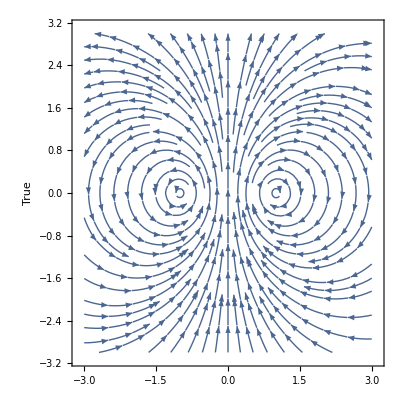

```mathematica
StreamPlot[{fx,fy},{x,-3,3},{y,-3,3},AxesLabel->True]
```

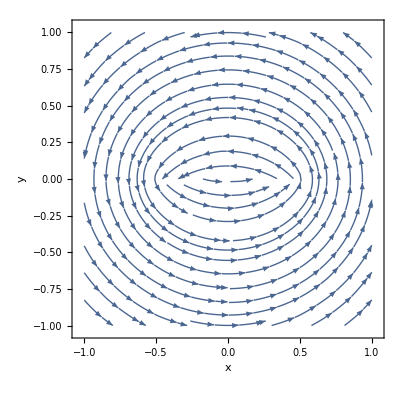

```mathematica
StreamPlot[{fx,fy},{x,-1,1},{y,-1,1}, Frame-> True, ]
```

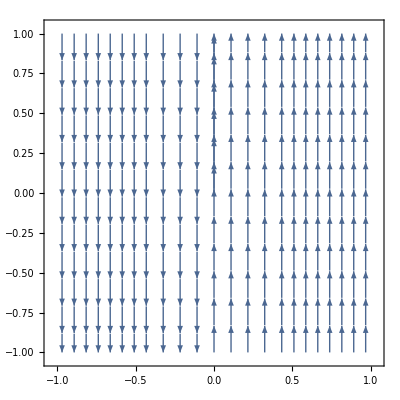

```mathematica
StreamPlot[{0,fy},{x,-1,1},{y,-1,1}]
```

```mathematica
F1 = Cross[{0,0,-1},{fx,fy,0}];
```

```mathematica
F2 = {F1[[1]],F1[[2]]}
```

{1/2 Log[((1/2+x)^2+y^2)/((-1/2+x)^2+y^2)],-ArcTan[(-1/2+x)/y]+ArcTan[(1/2+x)/y]}

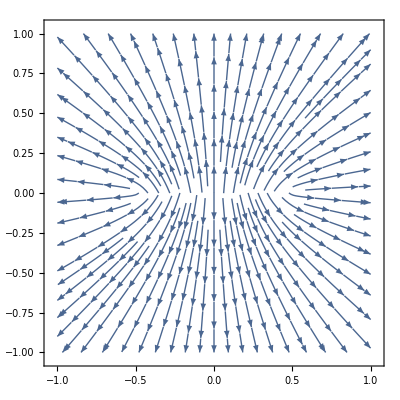

```mathematica
StreamPlot[F2,{x,-1,1},{y,-1,1}]
```

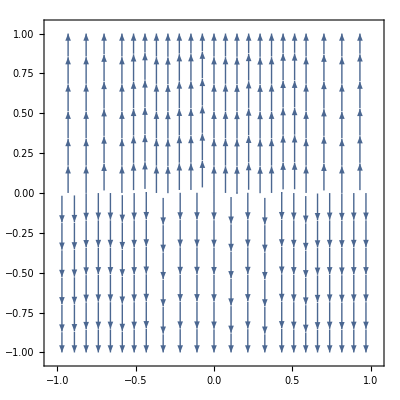

```mathematica
StreamPlot[{0,-fx},{x,-1,1},{y,-1,1}]
```

```mathematica
Integrate[x/(x^2+a^2),x]
```

1/2 Log[1+x^2]